## Plot EWS on parameter plane of Ricker

### Import data

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/ews_seasonal/models_ricker/ricker_seasonal2"];
```

```mathematica
rawB=Import["data_export/ews_stat_rvals/ews_b.csv"];
rawNB=Import["data_export/ews_stat_rvals/ews_nb.csv"];
```

### Variance

```mathematica
indexVar=Position[rawB[[1]],"Variance"][[1,1]];
```

```mathematica
rawB[[1]]
```

{rb,rnb,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,AIC fold,AIC hopf,AIC null,Params fold,Params hopf,Params null,Smax,Smax/Var}

```mathematica
varSeriesB=rawB[[2;;,{1,2,indexVar}]];
varSeriesNB=rawNB[[2;;,{1,2,indexVar}]];
```

```mathematica
(* Contour plot for breeding dynamics *)
plotVarB=ListContourPlot[varSeriesB,InterpolationOrder->1,
FrameLabel->{"rb","rnb"},
LabelStyle->11,
PlotRange->{{0,3},{-1,0},All},
PlotLegends->Placed[BarLegend[Automatic,
LegendLabel->Style["Breeding pop \n variance",11,GrayLevel[0.4]],
LegendMarkerSize->190],
Right],
ImageSize->250
];
```

```mathematica
(* Contour plot for non-breeding pop dynamics *)
plotVarNB=ListContourPlot[varSeriesNB,InterpolationOrder->1,
FrameLabel->{"rb","rnb"},
LabelStyle->11,
PlotRange->{{0,3},{-1,0},All},
PlotLegends->Placed[BarLegend[Automatic,
LegendLabel->Style["Non-breeding pop \n variance",11,GrayLevel[0.4]],
LegendMarkerSize->190],
Right],
ImageSize->250
];
```

### Coefficient of Variation

```mathematica
indexCv=Position[rawB[[1]],"Coefficient of variation"][[1,1]];
```

```mathematica
cvSeriesB=rawB[[2;;,{1,2,indexCv}]];
cvSeriesNB=rawNB[[2;;,{1,2,indexCv}]];
```

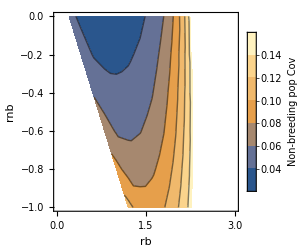

```mathematica
(* Contour plot for non-breeding pop dynamics *)
plotCvNB=ListContourPlot[cvSeriesNB,InterpolationOrder->1,
FrameLabel->{"rb","rnb"},
LabelStyle->11,
PlotRange->{{0,3},{-1,0},{0,0.15}},
PlotLegends->Placed[BarLegend[Automatic,
LegendLabel->Style["Non-breeding pop \n Cov",11,GrayLevel[0.4]],
LegendMarkerSize->190],
Right],
ImageSize->250
]
```

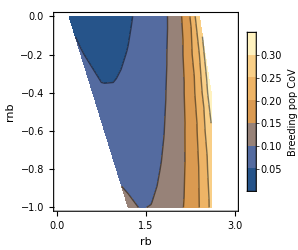

```mathematica
(* Contour plot for breeding dynamics *)
plotCvB=ListContourPlot[cvSeriesB,InterpolationOrder->1,
FrameLabel->{"rb","rnb"},
LabelStyle->11,
PlotRange->{{0,3},{-1,0},All},
PlotLegends->Placed[BarLegend[Automatic,
LegendLabel->Style["Breeding pop \n CoV",11,GrayLevel[0.4]],
LegendMarkerSize->190],
Right],
ImageSize->250
]
```

### Lag-1 Autocorrelation

```mathematica
indexAC1=Position[rawB[[1]],"Lag-1 AC"][[1,1]];
```

```mathematica
ac1SeriesB=rawB[[2;;,{1,2,indexAC1}]];
ac1SeriesNB=rawNB[[2;;,{1,2,indexAC1}]];
```

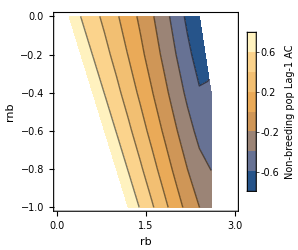

```mathematica
(* Contour plot for non-breeding pop dynamics *)
plotAc1NB=ListContourPlot[ac1SeriesNB,InterpolationOrder->1,
FrameLabel->{"rb","rnb"},
LabelStyle->11,
PlotRange->{{0,3},{-1,0},All},
PlotLegends->Placed[BarLegend[Automatic,
LegendLabel->Style["Non-breeding pop \n Lag-1 AC",11,GrayLevel[0.4]],
LegendMarkerSize->190],
Right],
ImageSize->250
]
```

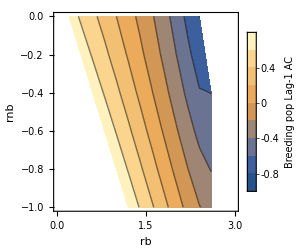

```mathematica
(* Contour plot for breeding dynamics *)
plotAc1B=ListContourPlot[ac1SeriesB,InterpolationOrder->1,
FrameLabel->{"rb","rnb"},
LabelStyle->11,
PlotRange->{{0,3},{-1,0},All},
PlotLegends->Placed[BarLegend[Automatic,
LegendLabel->Style["Breeding pop \n Lag-1 AC",11,GrayLevel[0.4]],
LegendMarkerSize->190],
Right],
ImageSize->250
]
```

### Lag-2 Autocorrelation

```mathematica
indexAC2=Position[rawB[[1]],"Lag-2 AC"][[1,1]];
```

```mathematica
ac2SeriesB=rawB[[2;;,{1,2,indexAC2}]];
ac2SeriesNB=rawNB[[2;;,{1,2,indexAC2}]];
```

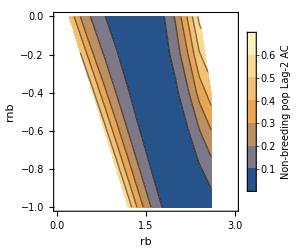

```mathematica
(* Contour plot for non-breeding pop dynamics *)
plotAc2NB=ListContourPlot[ac2SeriesNB,InterpolationOrder->1,
FrameLabel->{"rb","rnb"},
LabelStyle->11,
PlotRange->{{0,3},{-1,0},All},
PlotLegends->Placed[BarLegend[Automatic,
LegendLabel->Style["Non-breeding pop \n Lag-2 AC",11,GrayLevel[0.4]],
LegendMarkerSize->190],
Right],
ImageSize->250
]
```

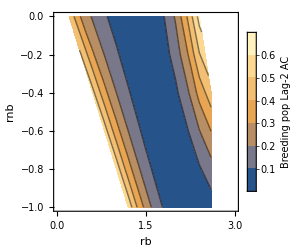

```mathematica
(* Contour plot for breeding dynamics *)
plotAc2B=ListContourPlot[ac2SeriesB,InterpolationOrder->1,
FrameLabel->{"rb","rnb"},
LabelStyle->11,
PlotRange->{{0,3},{-1,0},All},
PlotLegends->Placed[BarLegend[Automatic,
LegendLabel->Style["Breeding pop \n Lag-2 AC",11,GrayLevel[0.4]],
LegendMarkerSize->190],
Right],
ImageSize->250
]
```

### Smax/Var

```mathematica
indexSmax=Position[rawB[[1]],"Smax/Var"][[1,1]];
```

```mathematica
smaxSeriesB=rawB[[2;;,{1,2,indexSmax}]];
smaxSeriesNB=rawNB[[2;;,{1,2,indexSmax}]];
```

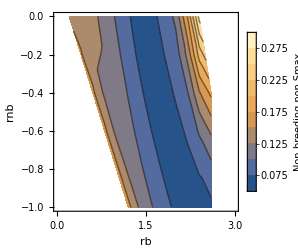

```mathematica
(* Contour plot for non-breeding pop dynamics *)
plotSmaxNB=ListContourPlot[smaxSeriesNB,InterpolationOrder->1,
FrameLabel->{"rb","rnb"},
LabelStyle->11,
PlotRange->{{0,3},{-1,0},All},
PlotLegends->Placed[BarLegend[Automatic,
LegendLabel->Style["Non-breeding pop \n Smax",11,GrayLevel[0.4]],
LegendMarkerSize->190],
Right],
ImageSize->250
]
```

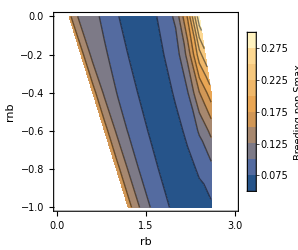

```mathematica
(* Contour plot for breeding dynamics *)
plotSmaxB=ListContourPlot[smaxSeriesB,InterpolationOrder->1,
FrameLabel->{"rb","rnb"},
LabelStyle->11,
PlotRange->{{0,3},{-1,0},All},
PlotLegends->Placed[BarLegend[Automatic,
LegendLabel->Style["Breeding pop \n Smax",11,GrayLevel[0.4]],
LegendMarkerSize->190],
Right],
ImageSize->250
]
```

### AIC

```mathematica
indexAicH=Position[rawB[[1]],"AIC hopf"][[1,1]];
```

```mathematica
aicHSeriesB=rawB[[2;;,{1,2,indexAicH}]];
aicHSeriesNB=rawNB[[2;;,{1,2,indexAicH}]];
```

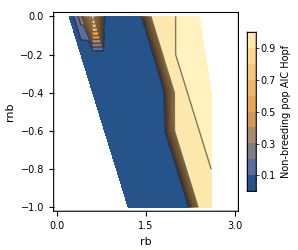

```mathematica
(* Contour plot for non-breeding pop dynamics *)
plotAicHNB=ListContourPlot[aicHSeriesNB,InterpolationOrder->1,
FrameLabel->{"rb","rnb"},
LabelStyle->11,
PlotRange->{{0,3},{-1,0},All},
PlotLegends->Placed[BarLegend[Automatic,
LegendLabel->Style["Non-breeding pop \n AIC Hopf",11,GrayLevel[0.4]],
LegendMarkerSize->190],
Right],
ImageSize->250
]
```

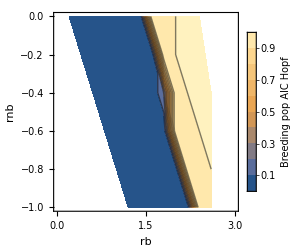

```mathematica
(* Contour plot for breeding dynamics *)
plotAicHB=ListContourPlot[aicHSeriesB,InterpolationOrder->1,
FrameLabel->{"rb","rnb"},
LabelStyle->11,
PlotRange->{{0,3},{-1,0},All},
PlotLegends->Placed[BarLegend[Automatic,
LegendLabel->Style["Breeding pop \n AIC Hopf",11,GrayLevel[0.4]],
LegendMarkerSize->190],
Right],
ImageSize->250
]
```